```mathematica
SetAttributes[tex,HoldFirst]
tex[exp_]:=TeXForm[HoldForm[exp]]
tf:=TableForm
mf:=MatrixForm
df:=Defer
```

```mathematica
Product[Sin[(π k/n)],{k,1,n-1}]
```

2^(1-n) n

```mathematica
Product[Gamma[k/n+1]/(k/n),{k,1,n-1}]//(TraditionalForm[Sqrt[#^2]]&)
```

√((2 π)^(n-1)/n)

```mathematica
ClearAll[Li];
Li[x_]:=Integrate[1/Log[y],{y,2,x}]
Li[20.]//N
```

8.86014

```mathematica
LogIntegral[20.]-LogIntegral[2.]
```

8.86014

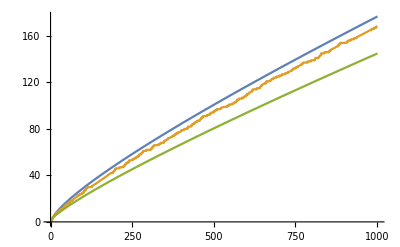

```mathematica
Plot[{LogIntegral[y]-LogIntegral[2],PrimePi[y],y/Log[y]},{y,2,1001},AxesOrigin->{0,0}]
```

```mathematica
D[Log[Log[y]],y]
```

1/(y Log[y])

```mathematica
ClearAll[f];
D[Log[f[x]],x]
```

f'[x]/f[x]

# Analytic Number Theory

Arithmetic

## Division

## Greatest Common Divisor

## Prime Numbers

### Prime Gap size n

#### Example

```mathematica
ClearAll[f,g,h,h1]
f[n_]:=Product[Prime[k],{k,1,n}]
g[n_]:=Table[{f[n]+2+k,FactorInteger[f[n]+2+k]},{k,0,n-1}]
h[n_]:=Table[{n!+2+k,FactorInteger[n!+2+k]},{k,0,n-1}]
h1[n_,m_]:=Table[{k+1,n!+2+k,FactorInteger[n!+2+k]},{k,0,m-1}]
h1[11,40]//TableForm
```

1 | 39916802 | 2 | 1
149 | 1
133949 | 1
2 | 39916803 | 3 | 1
13305601 | 1
3 | 39916804 | 2 | 2
59 | 1
79 | 1
2141 | 1
4 | 39916805 | 5 | 1
7983361 | 1
5 | 39916806 | 2 | 1
3 | 1
6652801 | 1
6 | 39916807 | 7 | 1
5702401 | 1
7 | 39916808 | 2 | 3
277 | 1
18013 | 1
8 | 39916809 | 3 | 2
31 | 1
173 | 1
827 | 1
9 | 39916810 | 2 | 1
5 | 1
3991681 | 1
10 | 39916811 | 11 | 2
329891 | 1
11 | 39916812 | 2 | 2
3 | 1
13 | 1
255877 | 1
12 | 39916813 | 199 | 1
200587 | 1
13 | 39916814 | 2 | 1
7 | 1
43 | 1
61 | 1
1087 | 1
14 | 39916815 | 3 | 1
5 | 1
19 | 1
227 | 1
617 | 1
15 | 39916816 | 2 | 4
17 | 1
101 | 1
1453 | 1
16 | 39916817 | 39916817 | 1
17 | 39916818 | 2 | 1
3 | 2
29 | 1
47 | 1
1627 | 1
18 | 39916819 | 39916819 | 1
19 | 39916820 | 2 | 2
5 | 1
1995841 | 1
20 | 39916821 | 3 | 1
7 | 2
37 | 1
41 | 1
179 | 1
21 | 39916822 | 2 | 1
11 | 1
23 | 1
78887 | 1
22 | 39916823 | 4057 | 1
9839 | 1
23 | 39916824 | 2 | 3
3 | 1
239 | 1
6959 | 1
24 | 39916825 | 5 | 2
13 | 1
263 | 1
467 | 1
25 | 39916826 | 2 | 1
103 | 1
193771 | 1
26 | 39916827 | 3 | 3
491 | 1
3011 | 1
27 | 39916828 | 2 | 2
7 | 1
1425601 | 1
28 | 39916829 | 39916829 | 1
29 | 39916830 | 2 | 1
3 | 1
5 | 1
241 | 1
5521 | 1
30 | 39916831 | 39916831 | 1
31 | 39916832 | 2 | 5
1247401 | 1
32 | 39916833 | 3 | 1
11 | 1
17 | 1
71153 | 1
33 | 39916834 | 2 | 1
19 | 1
619 | 1
1697 | 1
34 | 39916835 | 5 | 1
7 | 1
181 | 1
6301 | 1
35 | 39916836 | 2 | 2
3 | 2
1108801 | 1
36 | 39916837 | 39916837 | 1
37 | 39916838 | 2 | 1
13 | 1
73 | 1
21031 | 1
38 | 39916839 | 3 | 1
71 | 1
193 | 1
971 | 1
39 | 39916840 | 2 | 3
5 | 1
31 | 1
32191 | 1
40 | 39916841 | 167 | 1
239023 | 1

## Fundamental Theorem of Arithmetic

## Euclidean Algorithm

Tools

Arithmetic Functions and Dirichlet Series

The Prime Number Theorem

Dirichlet’s Theorem

Error Estimates and the Riemann Hypothesis

Temp

## Tmp-1